```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
(* Set of lattice parameters *)
lambdas={5.0, 4.0, 3.57, 3.45, 3.33, 3.23};
SourceNorms={0.0, 0.2540498,0.0,0.0,0.0,0.2733377};
VRdata={0.781, 0.708, 0.6499, 0.62134, 0.56809, 0.51202};
O0data={0.5577,0.6270,0.6590,0.66821,0.6775,0.6853};
O1data={0.4541,0.5464,0.5888,0.6009,0.6131,0.6234};
IncData={True,True,True,True,True,True};
(* Forming lists and plotting *)
GxPlots={}; mlPlots={};
For[iλ=1,iλ≤Length[lambdas],iλ++,
λ=lambdas[[iλ]];
SourceNorm = SourceNorms[[iλ]];
c=(iλ-1)/(Length[lambdas]-1);
Color1=RGBColor[c,0,1-c];
Color2=RGBColor[0.7+0.3c,0.7,0.7+0.3(1-c)];
(* Generating file names *)
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\scalars_d2_t32_s32_l"<>fsndig[λ,4]<>".dat";
If[FileExistsQ[ScalarFileName],
Print["λ = ",λ,", ",ScalarFileName];
GxData=GetConvergenceData[ScalarFileName,1,2,1,1.0,12];
MeanLinkData=GetConvergenceData[ScalarFileName,1,4,1,1.0,12];
MeanLinkExactData={{0.0,1-VRdata[[iλ]]},{0.5,O1data[[iλ]]},{1.0,O0data[[iλ]]}};
NFactor=(1-O0data[[iλ]])/(1-MeanLinkData[[1,2]]);
GxData=LinearTransformColumn[GxData,2,1-NFactor,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,2,1-NFactor,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,3,0.0,NFactor];
Print["NFactor = ",NFactor];
Gr2=Show[PlotWithErrors[GxData,Color1],PlotLabel->"<Gx>"];
GrExact=ListPlot[MeanLinkExactData,PlotStyle->{Color2,PointSize[0.02]},PlotRange->{{0.0,All},{0.0,All}}];
Gr3=Show[GrExact,PlotWithErrors[MeanLinkData,Color1],PlotLabel->"<link>",DisplayFunction->$DisplayFunction];
GrUnFiltered=Show[Gr3,ImageSize->800];
Print[GrUnFiltered];
];
];
```

λ = 3.23

a = 0.5, cc = 0.5, NN = 0.5

{{0.464576,0.525817},{-0.156254,-0.0561569},{0.159535,0.2206}}

{{-0.593502,-0.560498},{0.44123,0.480004},{0.777509,0.77976}}

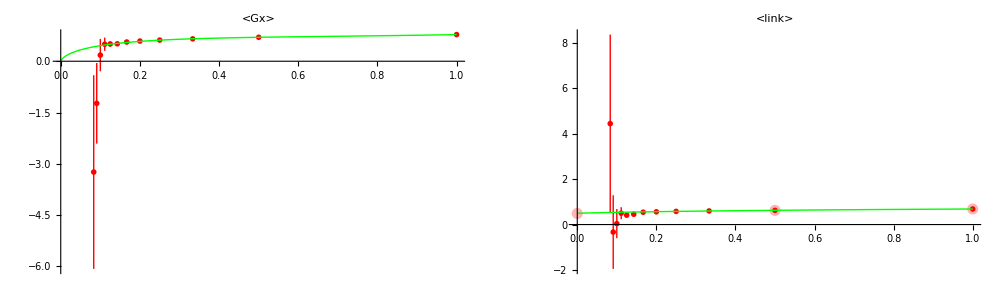

6696 points

Acceptance Rate = 0.546457 +/- 3.45677×10^-6

Mean return time = 125792. +/- 273.158

#################################################################################################################

a = 0.5, cc = 0.5, NN = 1.

{{0.476119,0.526883},{-0.128654,-0.0444459},{0.158522,0.209097}}

{{-0.589789,-0.548153},{0.441825,0.48837},{0.77707,0.780429}}

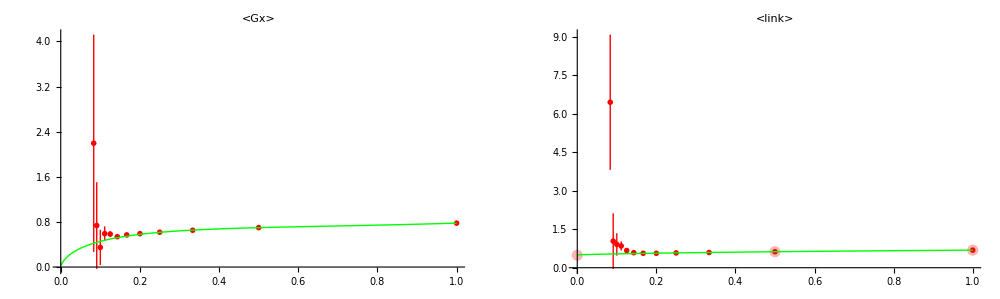

2445 points

Acceptance Rate = 0.593166 +/- 0.0000105103

Mean return time = 24173.9 +/- 47.2634

#################################################################################################################

a = 0.5, cc = 0.5, NN = 1.5

{{0.501577,0.529186},{-0.0907041,-0.0445806},{0.156195,0.183692}}

{{-0.596568,-0.535219},{0.438593,0.505761},{0.777118,0.782275}}

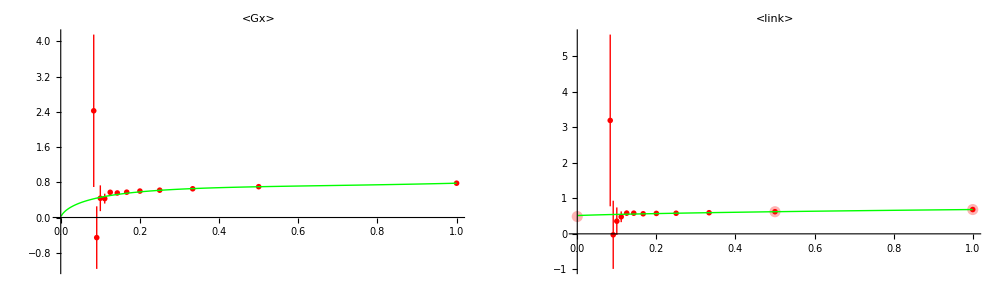

1698 points

Acceptance Rate = 0.595485 +/- 0.0000576833

Mean return time = 14378.7 +/- 29.2164

#################################################################################################################

a = 0.5, cc = 1., NN = 0.5

{{0.505519,0.508684},{-0.0809919,-0.0756431},{0.176625,0.179774}}

{{-0.590272,-0.538755},{0.44325,0.497682},{0.776908,0.781695}}

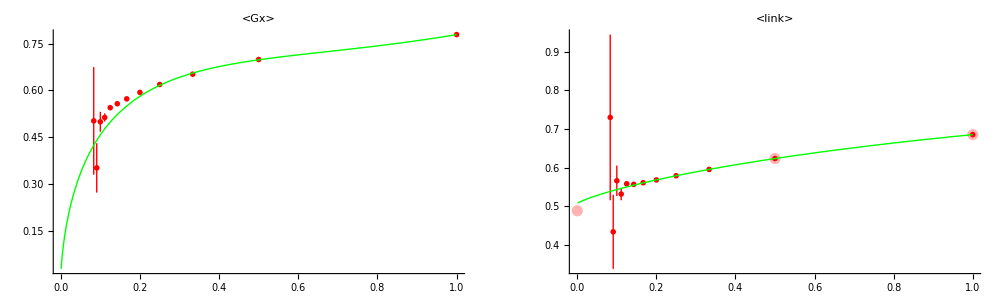

10717 points

Acceptance Rate = 0.737273 +/- 3.02441×10^-6

Mean return time = 830.565 +/- 0.215158

#################################################################################################################

a = 0.5, cc = 1., NN = 1.

{{0.504099,0.507759},{-0.0834466,-0.0770538},{0.177547,0.181183}}

{{-0.587226,-0.528122},{0.448571,0.507711},{0.776315,0.782306}}

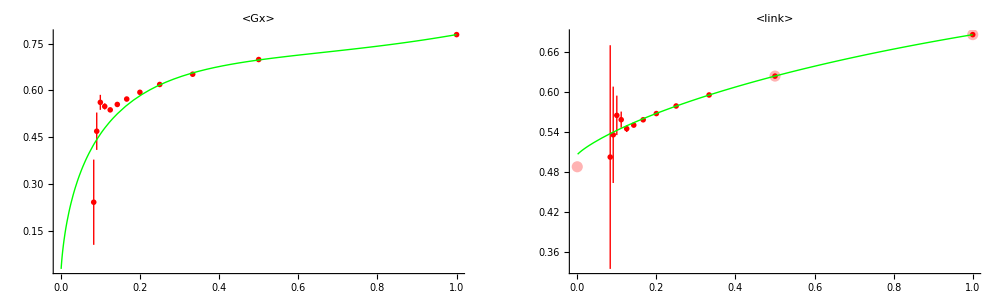

5993 points

Acceptance Rate = 0.765081 +/- 5.59304×10^-6

Mean return time = 301.532 +/- 0.0833217

#################################################################################################################

a = 0.5, cc = 1., NN = 1.5

{{0.504034,0.507554},{-0.0836331,-0.0773796},{0.17775,0.181244}}

{{-0.585022,-0.521443},{0.452389,0.514105},{0.77598,0.782674}}

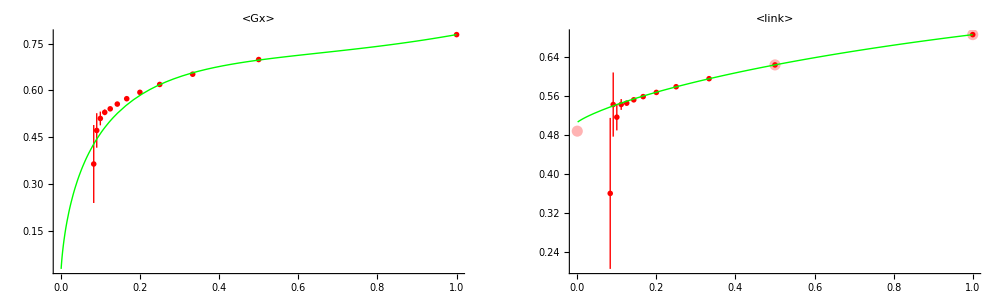

4985 points

Acceptance Rate = 0.772338 +/- 5.95952×10^-6

Mean return time = 222.175 +/- 0.0679236

#################################################################################################################

a = 0.5, cc = 1.5, NN = 0.5

{{0.503002,0.506206},{-0.0852811,-0.0795101},{0.179096,0.182274}}

{{-0.584493,-0.520308},{0.453224,0.514764},{0.775907,0.782794}}

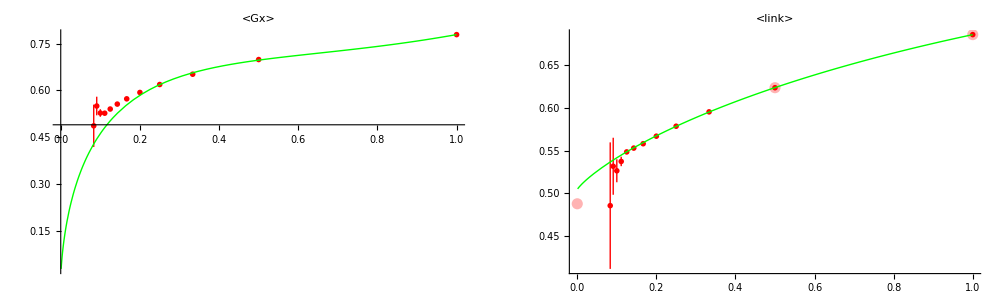

17983 points

Acceptance Rate = 0.716644 +/- 6.57961×10^-6

Mean return time = 143.982 +/- 0.025665

#################################################################################################################

a = 0.5, cc = 1.5, NN = 1.

{{0.504314,0.507},{-0.0831876,-0.0781874},{0.178307,0.180968}}

{{-0.580878,-0.509151},{0.459116,0.524866},{0.775298,0.78347}}

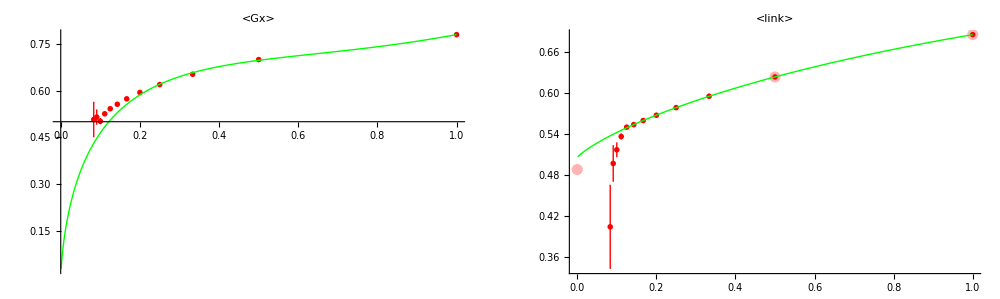

13599 points

Acceptance Rate = 0.717221 +/- 0.0000135429

Mean return time = 79.1948 +/- 0.0160107

#################################################################################################################

a = 0.5, cc = 1.5, NN = 1.5

{{0.503611,0.506114},{-0.0844305,-0.0797037},{0.179185,0.181664}}

{{-0.57907,-0.503649},{0.462213,0.530088},{0.775011,0.783817}}

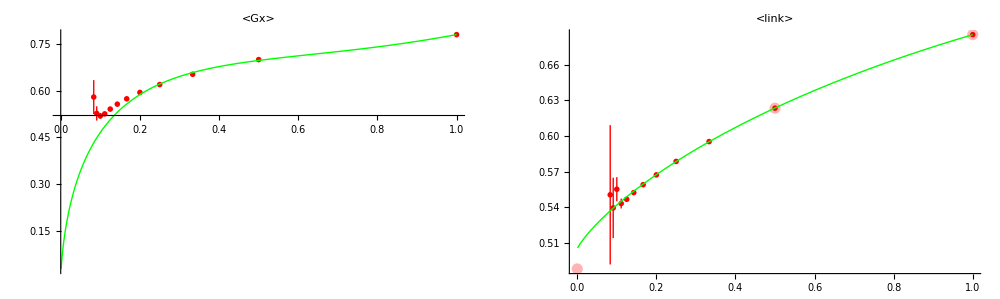

12612 points

Acceptance Rate = 0.717527 +/- 0.0000107221

Mean return time = 66.2072 +/- 0.0146445

#################################################################################################################

a = 1., cc = 0.5, NN = 0.5

{{0.553607,0.585619},{-0.0606868,-0.00220308},{0.0997765,0.13158}}

{{-0.571697,-0.467298},{0.536036,0.640513},{0.772347,0.783974}}

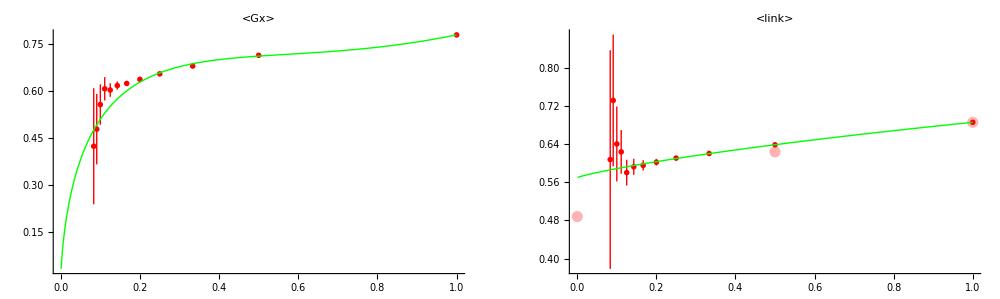

9703 points

Acceptance Rate = 0.529868 +/- 0.0000132036

Mean return time = 1.13564×10^6 +/- 9327.5

#################################################################################################################

a = 1., cc = 0.5, NN = 1.

{{0.482774,0.549992},{-0.131585,-0.00732626},{0.1355,0.202277}}

{{-0.579105,-0.482749},{0.476611,0.569251},{0.773682,0.784736}}

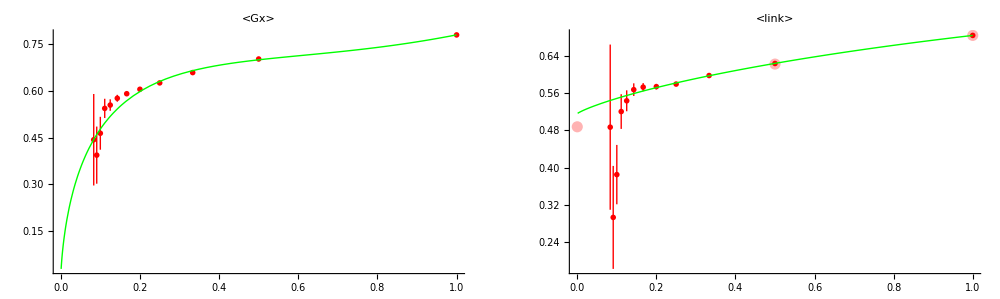

5274 points

Acceptance Rate = 0.590389 +/- 0.0000297324

Mean return time = 377333. +/- 2258.65

#################################################################################################################

a = 1., cc = 0.5, NN = 1.5

{{0.498734,0.53593},{-0.111392,-0.041656},{0.149419,0.186353}}

{{-0.584773,-0.482999},{0.467671,0.563061},{0.773008,0.78491}}

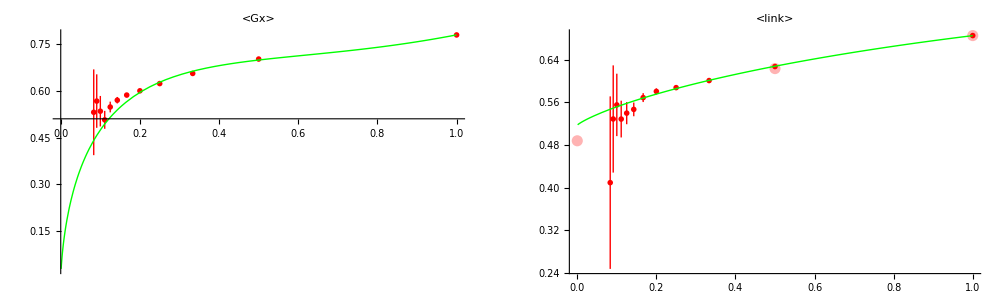

4289 points

Acceptance Rate = 0.612972 +/- 0.0000450219

Mean return time = 275674. +/- 1893.2

#################################################################################################################

a = 1., cc = 1., NN = 0.5

{{0.508662,0.517812},{-0.0824096,-0.0649852},{0.167526,0.176604}}

{{-0.575599,-0.463105},{0.478367,0.581293},{0.772669,0.786162}}

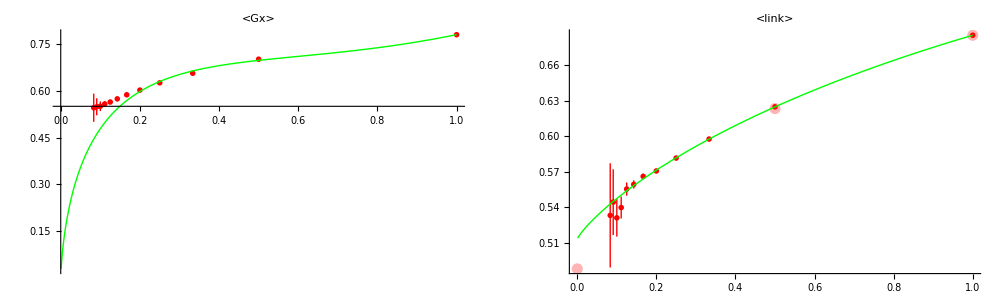

25902 points

Acceptance Rate = 0.611909 +/- 0.0000307148

Mean return time = 73846.4 +/- 226.699

#################################################################################################################

a = 1., cc = 1., NN = 1.

{{0.499535,0.509288},{-0.0937573,-0.0745685},{0.176014,0.185683}}

{{-0.571363,-0.470582},{0.477995,0.565996},{0.773102,0.785842}}

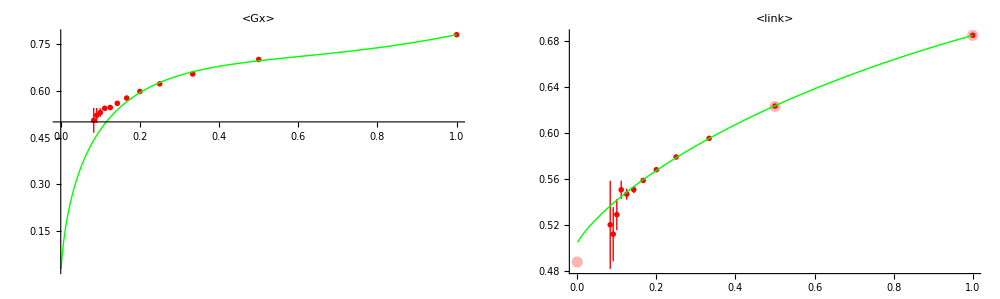

21501 points

Acceptance Rate = 0.610923 +/- 0.0000472625

Mean return time = 48964.4 +/- 160.11

#################################################################################################################

a = 1., cc = 1., NN = 1.5

{{0.511154,0.516764},{-0.0762829,-0.0650299},{0.16856,0.17412}}

{{-0.567263,-0.464599},{0.482545,0.57008},{0.7726,0.785958}}

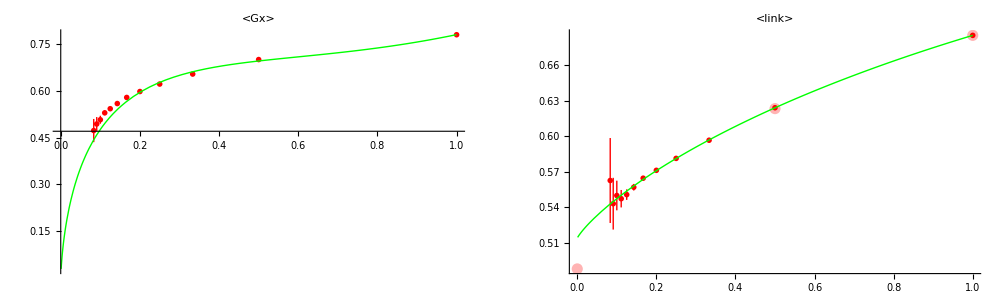

20878 points

Acceptance Rate = 0.611174 +/- 0.0000565261

Mean return time = 43700.4 +/- 200.284

#################################################################################################################

a = 1., cc = 1.5, NN = 0.5

{{0.513194,0.519831},{-0.0721918,-0.0587853},{0.165514,0.172093}}

{{-0.565122,-0.439327},{0.489992,0.597329},{0.771508,0.787747}}

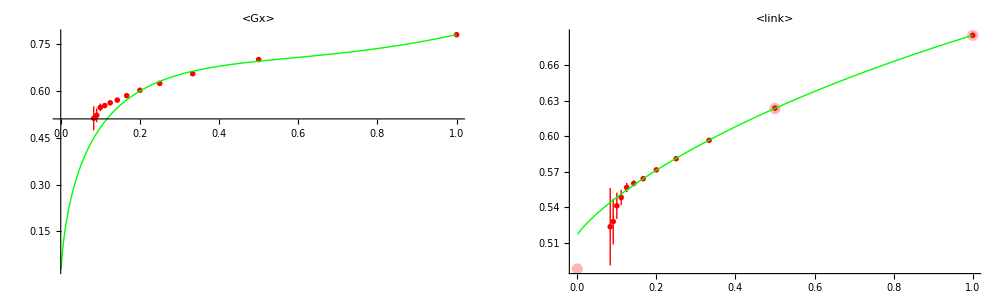

41867 points

Acceptance Rate = 0.499587 +/- 0.0000629017

Mean return time = 46677.9 +/- 1013.76

#################################################################################################################

a = 1., cc = 1.5, NN = 1.

{{0.508462,0.515848},{-0.080724,-0.0654029},{0.169504,0.176828}}

{{-0.566228,-0.447712},{0.487804,0.585855},{0.771676,0.787525}}

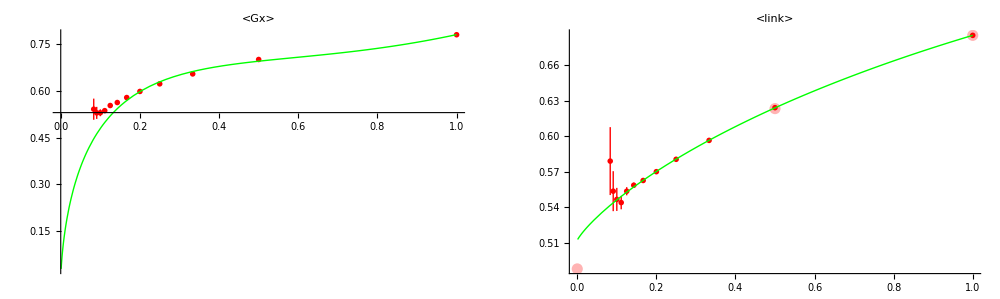

39104 points

Acceptance Rate = 0.486989 +/- 0.0000759101

Mean return time = 37295.4 +/- 1005.94

#################################################################################################################

a = 1., cc = 1.5, NN = 1.5

{{0.508104,0.514621},{-0.0806132,-0.0668987},{0.170703,0.177168}}

{{-0.562833,-0.430857},{0.493045,0.600507},{0.770701,0.788702}}

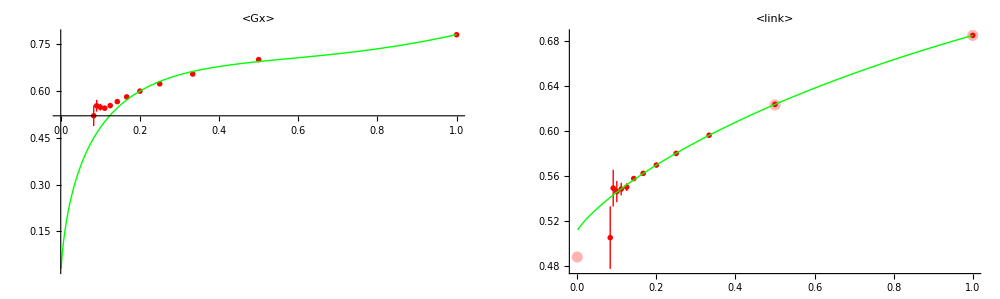

36369 points

Acceptance Rate = 0.48305 +/- 0.0000860544

Mean return time = 36666.7 +/- 840.653

#################################################################################################################

a = 1.5, cc = 0.5, NN = 0.5

{{0.631663,0.666966},{-0.0883392,-0.0140712},{0.0179712,0.0530273}}

{{-0.530952,-0.269233},{0.783651,0.998043},{0.75648,0.79965}}

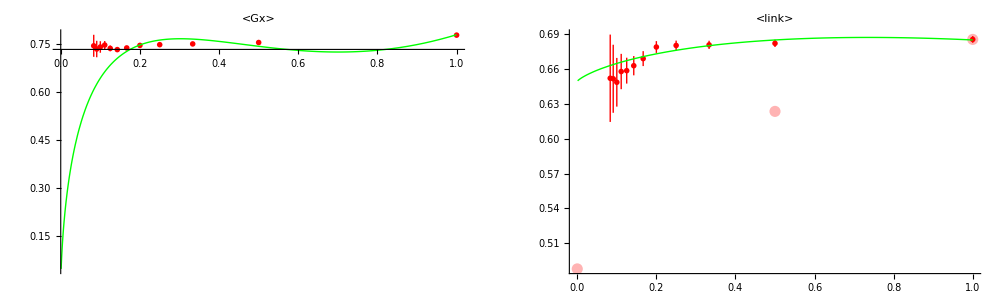

16014 points

Acceptance Rate = 0.540091 +/- 0.0000253562

Mean return time = 6.97192×10^6 +/- 47900.8

#################################################################################################################

a = 1.5, cc = 0.5, NN = 1.

{{0.604776,0.642126},{-0.063899,0.0143726},{0.0433802,0.0805067}}

{{-0.523784,-0.294872},{0.695972,0.885606},{0.75743,0.793535}}

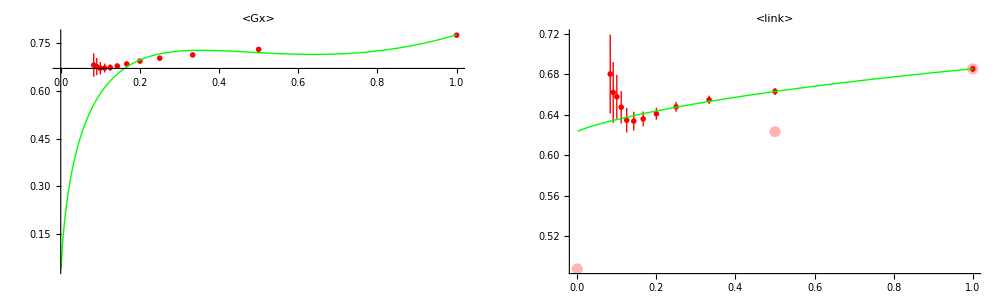

11889 points

Acceptance Rate = 0.597261 +/- 0.0000511078

Mean return time = 5.2155×10^6 +/- 48616.5

#################################################################################################################

a = 1.5, cc = 0.5, NN = 1.5

{{0.592458,0.605571},{-0.039004,-0.0111657},{0.0797834,0.0928299}}

{{-0.515132,-0.282638},{0.673877,0.862958},{0.759063,0.795531}}

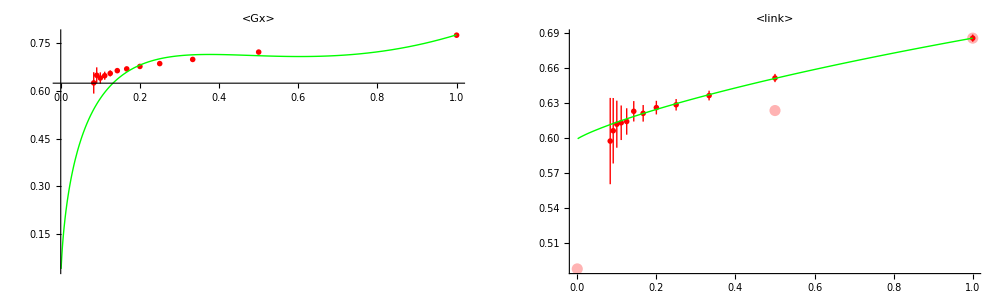

10536 points

Acceptance Rate = 0.61763 +/- 0.0000642018

Mean return time = 4.56072×10^6 +/- 48881.4

#################################################################################################################

a = 1.5, cc = 1., NN = 0.5

{{0.594672,0.601388},{-0.0150988,-0.000767861},{0.0838581,0.0905407}}

{{-0.505472,-0.282396},{0.662265,0.843817},{0.761249,0.795121}}

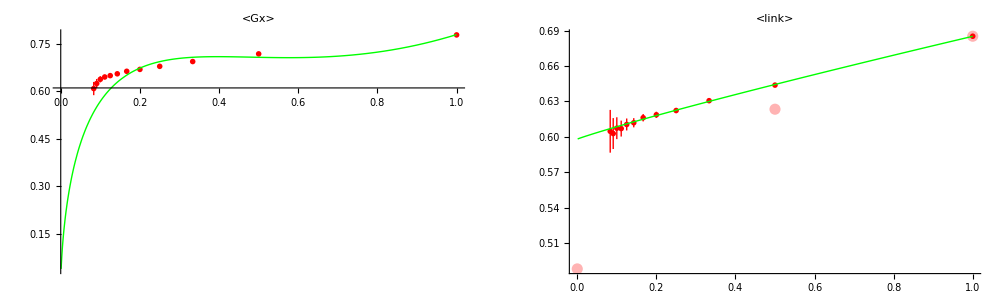

42885 points

Acceptance Rate = 0.496322 +/- 0.0000797799

Mean return time = 2.70309×10^6 +/- 18793.6

#################################################################################################################

a = 1.5, cc = 1., NN = 1.

{{0.565706,0.579963},{-0.044995,-0.013852},{0.10528,0.11949}}

{{-0.506877,-0.281843},{0.637813,0.815814},{0.761899,0.79662}}

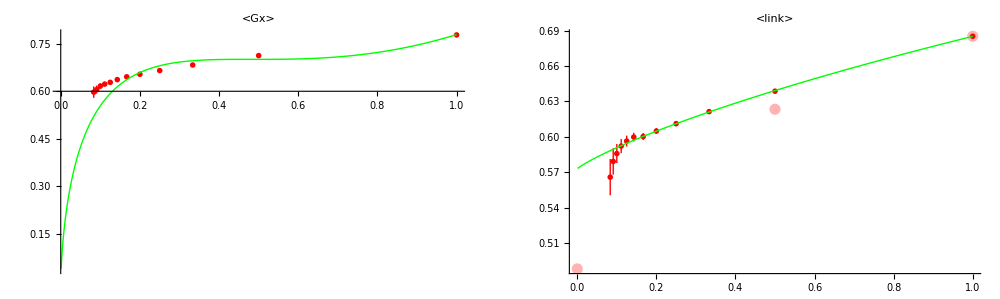

40213 points

Acceptance Rate = 0.487332 +/- 0.000100243

Mean return time = 2.25527×10^6 +/- 17979.4

#################################################################################################################

a = 1.5, cc = 1., NN = 1.5

{{0.56308,0.575635},{-0.0397159,-0.0118741},{0.109595,0.122124}}

{{-0.505827,-0.277226},{0.630933,0.808575},{0.761294,0.79706}}

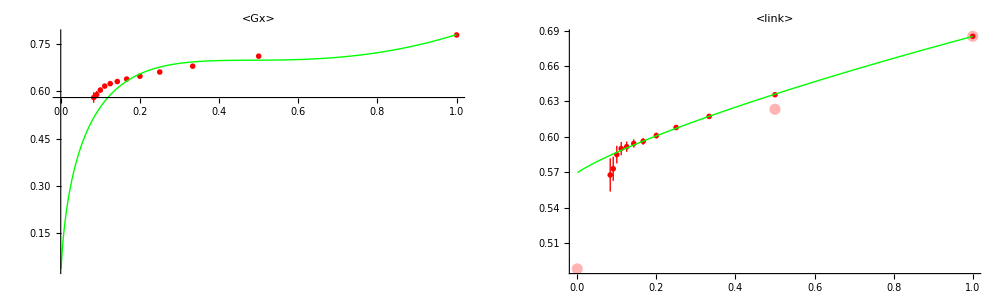

38037 points

Acceptance Rate = 0.485163 +/- 0.000110803

Mean return time = 2.04253×10^6 +/- 17898.6

#################################################################################################################

a = 1.5, cc = 1.5, NN = 0.5

{{0.578636,0.588866},{-0.0202233,0.00226854},{0.0963259,0.106522}}

{{-0.495575,-0.257866},{0.653118,0.839151},{0.761306,0.797967}}

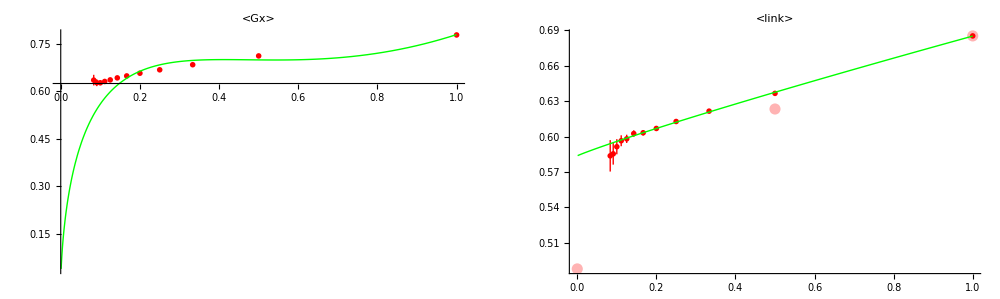

60936 points

Acceptance Rate = 0.383796 +/- 0.0000910486

Mean return time = 1.48789×10^6 +/- 11823.8

#################################################################################################################

a = 1.5, cc = 1.5, NN = 1.

{{0.577167,0.582635},{-0.0140497,-0.00173822},{0.102619,0.108081}}

{{-0.491907,-0.240113},{0.648559,0.840803},{0.760116,0.799778}}

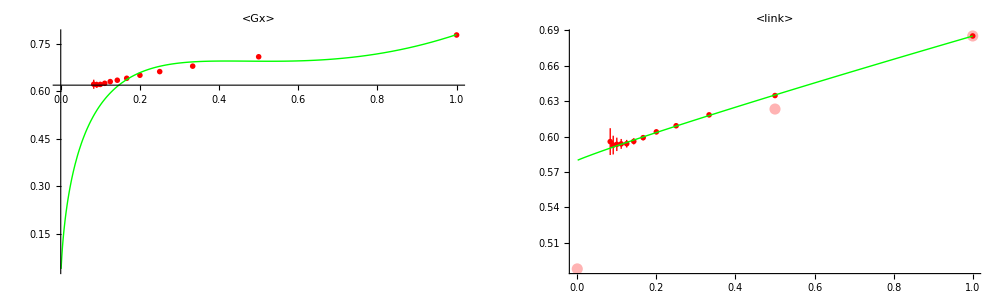

57043 points

Acceptance Rate = 0.373252 +/- 0.000100998

Mean return time = 1.25538×10^6 +/- 11291.1

#################################################################################################################

a = 1.5, cc = 1.5, NN = 1.5

{{0.573468,0.57835},{-0.0126217,-0.00148256},{0.106941,0.111825}}

{{-0.491881,-0.229745},{0.643613,0.841457},{0.759009,0.800636}}

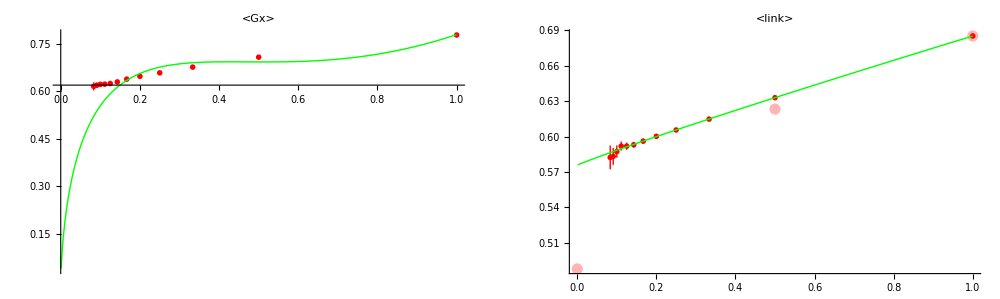

56728 points

Acceptance Rate = 0.370265 +/- 0.000102045

Mean return time = 1.11564×10^6 +/- 10655.3

#################################################################################################################

```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
Run["ssh-pageant rsync -v -z di72kov@lxlogin5.lrz.de:/home/hpc/b3101/di72kov/sd_metropolis/data/pcm_wc_mspace/scalars*.dat  /g/LAT/sd_metropolis/data/pcm_wc_mspace/"];
Run["ssh-pageant rsync -v -z di72kov@lxlogin5.lrz.de:/home/hpc/b3101/di72kov/sd_metropolis/data/pcm_wc_mspace/metropolis_stat*.dat  /g/LAT/sd_metropolis/data/pcm_wc_mspace/"];
lambdas={5.0, 4.0, 3.57, 3.45, 3.33, 3.23};
VRdata={0.781, 0.708, 0.6499, 0.62134, 0.56809, 0.51202};
O0data={0.5577,0.6270,0.6590,0.66821,0.6775,0.6853};
O1data={0.4541,0.5464,0.5888,0.6009,0.6131,0.6234};
iλ=6;
λ=lambdas[[iλ]]; 
c=(iλ-1)/(Length[lambdas]-1);
Color1=RGBColor[c,0,1-c];
Color2=RGBColor[0.7+0.3c,0.7,0.7+0.3(1-c)];
Print["λ = ",λ];
Do[
(*Manipulate[*)
Print["a = ",a,", cc = ",cc,", NN = ",NN];
Suffix="d2_t32_s32_l"<>fsndig[λ,4]<>"_a"<>fsndig[a,2]<>"_c"<>fsndig[cc,2]<>"_n"<>fsndig[NN,2];
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\scalars_"<>Suffix<>".dat";
McStatFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\metropolis_stat_"<>Suffix<>".dat";
If[FileExistsQ[ScalarFileName] && FileExistsQ[McStatFileName] ,
(* Analyzing the data *)
GxData=GetConvergenceData[ScalarFileName,1,2,1,1.0,13];
MeanLinkData=GetConvergenceData[ScalarFileName,1,4,1,1.0,13];
NFactor=(1-O0data[[iλ]])/(1-MeanLinkData[[1,2]]);
GxData=LinearTransformColumn[GxData,2,1-NFactor,NFactor];
GxData=LinearTransformColumn[GxData,3,0.0,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,2,1-NFactor,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,3,0.0,NFactor];
(* Fitting the data *)
MeanLinkDataToFit=Transpose[MeanLinkData];
FitWeights=MeanLinkDataToFit[[3]];
MeanLinkDataToFit=Transpose[Take[MeanLinkDataToFit,2]];
NMF=NonlinearModelFit[MeanLinkDataToFit,AA+BB x Log[x] +CC  x,{AA,BB,CC},x,Weights->1/FitWeights^2];
MeanLinkFit=NMF["BestFitParameters"];
Print[NMF["ParameterConfidenceIntervals"]];
GxDataToFit=Transpose[GxData];
FitWeights=GxDataToFit[[3]];
GxDataToFit=Transpose[Take[GxDataToFit,2]];
NMF=NonlinearModelFit[GxDataToFit,AA x Log[x]+ BB x Log[x]^2 +CC  x,{AA,BB,CC},x,Weights->1/FitWeights^2];
GxFit=NMF["BestFitParameters"];
Print[NMF["ParameterConfidenceIntervals"]];
(* Plotting *)
MeanLinkExactData={{0.0,1-VRdata[[iλ]]},{0.5,O1data[[iλ]]},{1.0,O0data[[iλ]]}};
Gr2=Show[PlotWithErrors[GxData,Color1],PlotLabel->"<Gx>"];
GrGxFit=Plot[(AA x Log[x] +BB x Log[x]^2 +CC  x)/.GxFit,{x,0.001,1.0},PlotStyle->{Green},PlotRange->All];
GrExact=ListPlot[MeanLinkExactData,PlotStyle->{Color2,PointSize[0.02]},PlotRange->{{0.0,All},{0.0,All}}];
GrMeanLinkFit=Plot[(AA+BB x Log[x] +CC  x)/.MeanLinkFit,{x,0.001,1.0},PlotStyle->{Green},PlotRange->All];
Gr3=Show[GrExact,PlotWithErrors[MeanLinkData,Color1],GrMeanLinkFit,PlotLabel->"<link>"];
Print[GraphicsGrid[{{Show[Gr2,GrGxFit],Gr3}},ImageSize->1000]];
(* Analyzing the algorithm performance *)
McStatData=Transpose[Import[McStatFileName,"Table"]];
Print[Length[McStatData[[1]]]," points"];
PrintStatistics[McStatData[[1]],"Acceptance Rate"];
PrintStatistics[McStatData[[9]],"Mean return time"];
Print["#################################################################################################################"];
];
,{a,{0.5,1.0,1.5}},{cc,{0.5,1.0,1.5}},{NN,{0.5,1.0,1.5}}
];
```

a = 1., cc = 1., NN = 1.

NFactor = 12191.1

{0.6853,0.623694,0.595636,0.579373,0.568339,0.558986,0.550973,0.54705,0.550872,0.529253,0.512202,0.520361}

(0.00805677 | 0.00920734 | 0.0095414 | 0.00967117 | 0.00966386 | 0.00957785 | 0.00968851 | 0.00931676 | 0.00978722 | 0.00962611 | 0.0108626 | 0.013333
0.00920734 | 0.0118264 | 0.0125854 | 0.0129008 | 0.0129803 | 0.012924 | 0.0131541 | 0.0125552 | 0.0126443 | 0.0121762 | 0.0130144 | 0.0162582
0.0095414 | 0.0125854 | 0.0158809 | 0.0169322 | 0.0173858 | 0.0175511 | 0.0180909 | 0.0174457 | 0.0176387 | 0.0170275 | 0.0180896 | 0.0216742
0.00967117 | 0.0129008 | 0.0169322 | 0.0232053 | 0.0252891 | 0.0261307 | 0.0274045 | 0.0274009 | 0.0277504 | 0.0276161 | 0.0318995 | 0.0385254
0.00966386 | 0.0129803 | 0.0173858 | 0.0252891 | 0.0396097 | 0.0442634 | 0.0472569 | 0.0480009 | 0.0489003 | 0.050672 | 0.0569391 | 0.0632811
0.00957785 | 0.012924 | 0.0175511 | 0.0261307 | 0.0442634 | 0.0804728 | 0.0933477 | 0.0988249 | 0.100707 | 0.105231 | 0.116006 | 0.125861
0.00968851 | 0.0131541 | 0.0180909 | 0.0274045 | 0.0472569 | 0.0933477 | 0.18941 | 0.220389 | 0.232574 | 0.247574 | 0.257665 | 0.286082
0.00931676 | 0.0125552 | 0.0174457 | 0.0274009 | 0.0480009 | 0.0988249 | 0.220389 | 0.486157 | 0.576207 | 0.62646 | 0.656951 | 0.723505
0.00978722 | 0.0126443 | 0.0176387 | 0.0277504 | 0.0489003 | 0.100707 | 0.232574 | 0.576207 | 1.33551 | 1.61525 | 1.74228 | 1.82531
0.00962611 | 0.0121762 | 0.0170275 | 0.0276161 | 0.050672 | 0.105231 | 0.247574 | 0.62646 | 1.61525 | 3.9786 | 4.78161 | 5.23268
0.0108626 | 0.0130144 | 0.0180896 | 0.0318995 | 0.0569391 | 0.116006 | 0.257665 | 0.656951 | 1.74228 | 4.78161 | 11.9836 | 14.5357
0.013333 | 0.0162582 | 0.0216742 | 0.0385254 | 0.0632811 | 0.125861 | 0.286082 | 0.723505 | 1.82531 | 5.23268 | 14.5357 | 31.641) {40.8657,5.76412,2.00621,0.713237,0.260148,0.10494,0.0464198,0.020011,0.00791859,0.00297351,0.0011291,0.00039734}

{p1→0.467355,p2→0.228712,p3→-0.0107722}

(0.0000159497 | -0.0000367082 | 0.0000212031
-0.0000367082 | 0.0000893031 | -0.0000525056
0.0000212031 | -0.0000525056 | 0.0000311432)

Mean plaquette is between 0.463361 and 0.471349 (0.854534 %)

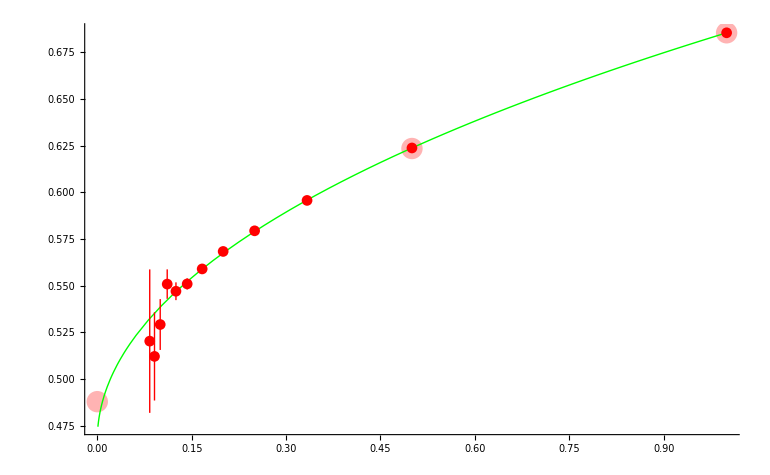

```mathematica
(* Fitting taking into account the covariance matrix *)
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
lambdas={5.0, 4.0, 3.57, 3.45, 3.33, 3.23};
VRdata={0.781, 0.708, 0.6499, 0.62134, 0.56809, 0.51202};
O0data={0.5577,0.6270,0.6590,0.66821,0.6775,0.6853};
O1data={0.4541,0.5464,0.5888,0.6009,0.6131,0.6234};
iλ=6;
λ=lambdas[[iλ]]; 
MeanLinkExactData={{0.0,1-VRdata[[iλ]]},{0.5,O1data[[iλ]]},{1.0,O0data[[iλ]]}};
mmax=12;
a=1.0; cc=1.0; NN = 1.0;
Print["a = ",a,", cc = ",cc,", NN = ",NN];
Suffix="d2_t32_s32_l"<>fsndig[λ,4]<>"_a"<>fsndig[a,2]<>"_c"<>fsndig[cc,2]<>"_n"<>fsndig[NN,2];
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\scalars_"<>Suffix<>".dat";
ScalarData=Import[ScalarFileName,"Table"];
LinkAverage=Table[0.0,{m,1,mmax}];
LinkCorrelation=Table[0.0,{m1,1,mmax},{m2,1,mmax}];
DataCounter=0;
For[i=1,i≤Length[ScalarData],i+=mmax,
For[m1=1,m1≤mmax,m1++,
mcheck=ScalarData[[i+m1-1,1]]+1;
If[mcheck≠m1,Print["Alarma!!!"];];
LinkAverage[[m1]]+=ScalarData[[i+m1-1,4]];
For[m2=1,m2≤mmax,m2++,
LinkCorrelation[[m1,m2]]+=ScalarData[[i+m1-1,4]] ScalarData[[i+m2-1,4]];
];
];
DataCounter++;
];
LinkAverage /= DataCounter;
LinkCorrelation=LinkCorrelation/DataCounter - KroneckerProduct[LinkAverage,LinkAverage];
NFactor=(O0data[[iλ]]-1)/LinkAverage[[1]];
Print["NFactor = ",NFactor];
LinkAverage=1+NFactor LinkAverage;
LinkCorrelation*=NFactor^2;
(* Table of conventional errors *)
LinkErrors=Table[√(LinkCorrelation[[m,m]]/(DataCounter-1)),{m,1,mmax}];
(* Defining chi2 for fitting *)
Clear[x]; 
FitFuncs={1,√x,x};(*{1,x Log[x], x, x Log[x]^2};*)
parlist=Table[Symbol["p"<>ToString[i]],{i,1,Length[FitFuncs]}];
F[x_]:=Sum[parlist[[i]] FitFuncs[[i]],{i,1,Length[FitFuncs]}];
LCI=Inverse[LinkCorrelation];
Chi2[pars_]:=Module[{Y0,m,i},
Y0=Table[Sum[(pars[[i]] FitFuncs[[i]])/.{x->1/m},{i,1,Length[FitFuncs]}],{m,1,mmax}];
0.5/(DataCounter-1)(LinkAverage-Y0).LCI.(LinkAverage-Y0)
];
Print[LinkAverage];
Print[MatrixForm[LinkCorrelation]," ",Eigenvalues[LinkCorrelation]];
FitVals=NMinimize[Chi2[parlist],parlist][[2]];
Print[FitVals];
(* Getting the parameter Jacobian *)
P2=(DataCounter-1) Table[Sum[(FitFuncs[[i]]/.{x->1/m1})LCI[[m1,m2]] (FitFuncs[[j]]/.{x->1/m2}),{m1,1,mmax},{m2,1,mmax}],{i,1,Length[FitFuncs]},{j,1,Length[FitFuncs]}];
P2=Inverse[P2];
Print[MatrixForm[P2]];
Print["Mean plaquette is between ",(p1/.FitVals )- √P2[[1,1]]," and ",(p1/.FitVals) + √P2[[1,1]]," (", 100.0 √P2[[1,1]]/(p1/.FitVals)," %)"];
(* Plotting *)
LinkAverageToPlot=Transpose[{Table[1/m,{m,1,mmax}],LinkAverage,LinkErrors}];
Gr1=PlotWithErrors[LinkAverageToPlot,Red];
Gr2=ListPlot[MeanLinkExactData,PlotStyle->{RGBColor[1.0,0.7,0.7],PointSize[0.02]},PlotRange->{{0.0,All},{0.0,All}}];
Gr3=Plot[F[x]/.FitVals,{x,0.001,1.0},PlotStyle->{Green}];
Show[Gr2,Gr3,Gr1]
```

a = 1., cc = 1., NN = 1.

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o0.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o1.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o2.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o3.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o4.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o5.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o6.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o7.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o8.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o9.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o10.dat

C:\DATA\pcm_wc_mspace_raw_data\Gxy_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00_o11.dat

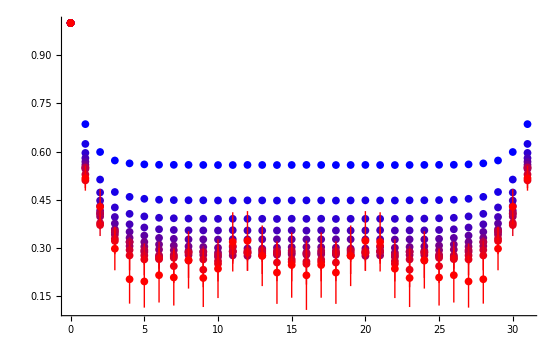

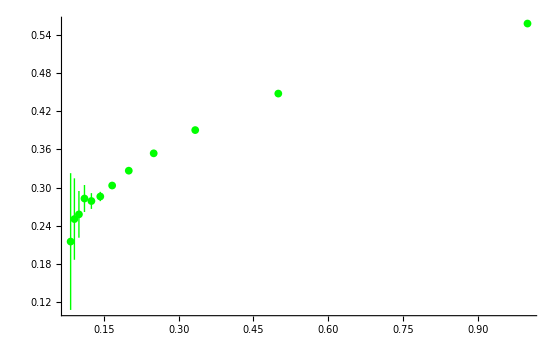

```mathematica
(* Looking at the full correlators *)
$HistoryLength=0;
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
mmax=12; λ=3.23;LS=32; NFactor=12189.0;
a=1.0; cc=1.0; NN = 1.0;
Print["a = ",a,", cc = ",cc,", NN = ",NN];
Suffix="d2_t32_s32_l"<>fsndig[λ,4]<>"_a"<>fsndig[a,2]<>"_c"<>fsndig[cc,2]<>"_n"<>fsndig[NN,2];
Run["ssh-pageant rsync -v -z di72kov@lxlogin5.lrz.de:/home/hpc/b3101/di72kov/sd_metropolis/data/pcm_wc_mspace/Gxy_"<>Suffix<>"_o*.dat /c/DATA/pcm_wc_mspace_raw_data/"];
GrS={};
MidPoints={};
For[m=1,m≤mmax,m++,
r=(m-1)/(mmax-1);
GxyDataFile="C:\\DATA\\pcm_wc_mspace_raw_data\\Gxy_"<>Suffix<>"_o"<>ToString[m-1]<>".dat";
Print[GxyDataFile];
GxyData=Import[GxyDataFile,"Table"];
aGxy=Table[0.0,{x,1,LS}];
dGxy=Table[0.0,{x,1,LS}];
DataCounter=0;
For[i=1,i≤Length[GxyData],i+=LS,
mGxy=Table[GxyData[[i+p,2]],{p,0,LS-1}];
cGxy=Re[Fourier[mGxy,FourierParameters->{1,1}]];
aGxy+=cGxy;
dGxy+=cGxy^2;
DataCounter++;
];
aGxy/=DataCounter; dGxy =√((dGxy/DataCounter - aGxy^2)/(DataCounter-1));
GxyToPlot=Transpose[{Table[x,{x,0,LS-1}],1+NFactor aGxy,NFactor dGxy}];
AppendTo[MidPoints,{1/m,1+NFactor aGxy[[LS/2+1]],NFactor dGxy[[LS/2+1]]}];
Gr1=PlotWithErrors[GxyToPlot,RGBColor[r,0,1-r]];
(*Print[Show[Gr1]];*)
AppendTo[GrS,Gr1];
];
Show[GrS]
PlotWithErrors[MidPoints,Green]
```

```mathematica
Fourier[{1,0,0,0,0},FourierParameters->{1,1}]
```

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

```mathematica
N[(14^4 8)/(1024 1024)]
```

0.293091

```mathematica
N[1/3.23]
```

0.309598